Análise de Gráficos - Bolhas em Cilindro

Inputs:
- Número de Bolhas
- Raio do Cilindro
- Altura do Cilindro

Outputs:
- Visualização 2D/3D das bolhas no cilindro (o raio das bolhas vai até 0.01r até 0.5r)
- F = (n° de pixels das bolhas)/(n° de pixels do cilindro)
- Gráfico (volume das bolhas/D^3) x (F*(D*h))/D^2)
- fração de área ocupada pelas bolhas x fração de volume ocupado

```mathematica
Cilindro[r_,h_] := ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{θ,0,π},{z,0,h},Mesh->None,PlotStyle->Directive[Opacity[1],Red],BoundaryStyle->Directive[Black,Thin],ViewPoint->{0,-∞,0},Lighting->{{"Ambient",Red}}]
```

```mathematica
Cilindro2[r_,h_] := ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{θ,0,2π},{z,0,h},Mesh->None,PlotStyle->{Opacity[0.5],LightGray}]
```

```mathematica
Bolhas[n_, raio_, h_] := 
(bubbles = {{},{}};
For[j=0,j<  n, j++;
rvalue= RandomReal[{0.01raio,0.5raio}];
Rzone= RandomReal[raio-rvalue];
θ = RandomReal[2π];
xvalue = Rzone Cos[θ];
yvalue = Rzone Sin[θ];
zvalue = RandomReal [{rvalue,h-rvalue}];

If[Length[bubbles⟦2⟧]==0, AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue];j=j+1];

touch={};
For[k=0,k< Length[bubbles⟦1⟧],k++;
pbubble = bubbles⟦1,k⟧;
rbubble = bubbles⟦2,k⟧;
Δx = xvalue - pbubble⟦1⟧;Δy = yvalue - pbubble⟦2⟧;Δz = zvalue - pbubble⟦3⟧;
If[√(Δx^2+Δy^2+Δz^2)> (rvalue + rbubble), AppendTo[touch,0], AppendTo[touch,1]]];

If[FreeQ[touch,1], AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue],j= j-1]];
AppendTo[bubbles,1/(π  raio^2  h)(Total[Table[4/3 π(bubbles⟦2,i⟧)^3,{i,1,Length[bubbles⟦2⟧]}]])];
AppendTo[bubbles,(Total[Table[π(bubbles⟦2,i⟧)^2,{i,1,Length[bubbles⟦2⟧]}]])];
bubbles)
```

```mathematica
VistaBolhas2D[n_,r_,h_]:= (bolhas = Bolhas[n,r,h];
Show[Graphics3D[{Opacity[1],Black,Sphere[bolhas⟦1⟧,bolhas⟦2⟧],ViewPoint->{0,- Infinity, 0}}],
Cilindro[r,h],Lighting->{{"Ambient",Red}},ViewPoint->{0,-∞,0}])
```

```mathematica
VistaBolhas3D[n_,r_,h_]:= (bolhas = Bolhas[n,r,h];Show[Graphics3D[{Opacity[0.5],Sphere[bolhas⟦1⟧,bolhas⟦2⟧]}],
Cilindro2[r,h]])
```

```mathematica
img1=ColorSeparate[Image[VistaBolhas2D[30,1,3],"Byte",ImageResolution->300]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
myLevels={ImageLevels[img1[[1]],2],ImageLevels[img1[[4]],2]}
```

{{{0.,696671},{0.5,1464529}},{{0.,164619},{0.5,1996581}}}

```mathematica
N[myLevels[[1,2,2]]/myLevels[[2,2,2]]]
```

0.733518

Ao criar x cilindros com as mesmas especificações [n, raio, h], chegamos ao seguinte tipo de gráfico e processo:

```mathematica
lista2={};
listaproj={};
grafico [n_,r_,h_]:=
(img=ColorSeparate[Image[VistaBolhas2D[n,r,h],"Byte",ImageResolution->300]];
myLevels={ImageLevels[img⟦1⟧,2],ImageLevels[img⟦4⟧,2]};
vazio=1-N[myLevels[[1,2,2]]/myLevels[[2,2,2]]];
AppendTo[listaproj, {bubbles⟦3⟧/(2*r)^3,(vazio*(2*r*h))/(2*r)^2}];
listaproj)
```

```mathematica
Do[lista2 = grafico[10,1,3],{100}]
```

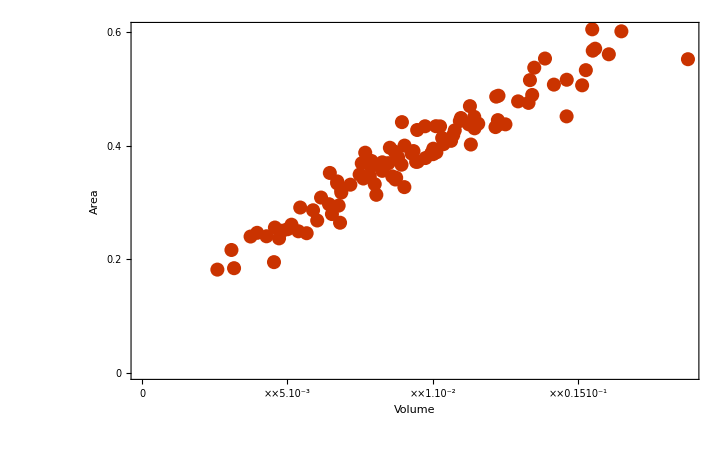

```mathematica
ListPlot[lista2,PlotTheme->"Web",FrameLabel->{{HoldForm[Area],None},{HoldForm[Volume],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
lista2 = {}
```

{}

```mathematica
listaproj={}
```

{}

```mathematica
Do[lista2= grafico[20,3,9],{80}]
```

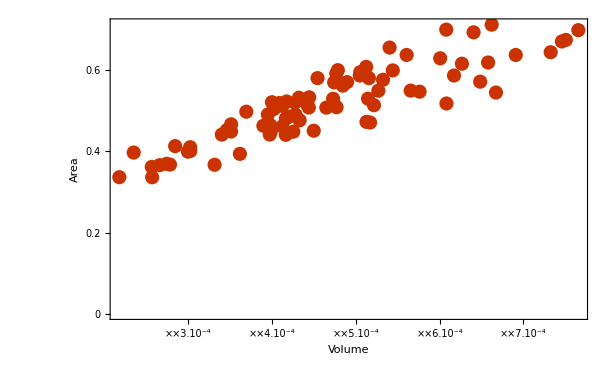

```mathematica
ListPlot[lista2,PlotTheme->"Web",FrameLabel->{{HoldForm[Area],None},{HoldForm[Volume],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Ao criar x cilindros variando somente o número de bolhas produzido, temos:

```mathematica
lista2={};
listaproj={};
grafico [n_,r_,h_]:=
(img=ColorSeparate[Image[VistaBolhas2D[n,r,h],"Byte",ImageResolution->300]];
myLevels={ImageLevels[img⟦1⟧,2],ImageLevels[img⟦4⟧,2]};
vazio=1-N[myLevels[[1,2,2]]/myLevels[[2,2,2]]];
AppendTo[listaproj, {bubbles⟦3⟧/(2*r)^3,(vazio*(2*r*h))/(2*r)^2}];
listaproj)
```

```mathematica
Do[lista2=grafico[i,1,3],{i, Range[1,20,1]}]
```

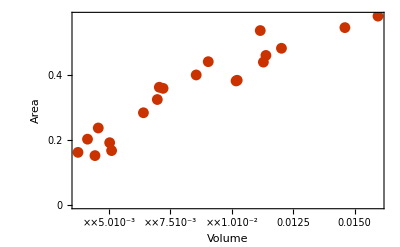

```mathematica
ListPlot[lista2,PlotTheme->"Web",FrameLabel->{{HoldForm[Area],None},{HoldForm[Volume],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
lista2={}
```

{}

```mathematica
listaproj = {}
```

{}

```mathematica
Do[lista2=grafico[i,4,10],{i,Range[1,25,1]}]
```

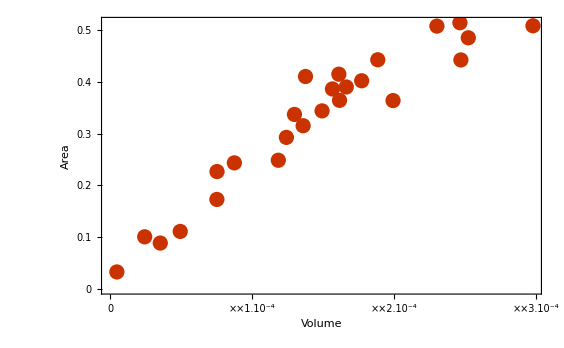

```mathematica
ListPlot[lista2,PlotTheme->"Web",FrameLabel->{{HoldForm[Area],None},{HoldForm[Volume],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Ao criar x cilindros variando as dimensões do cilindro, temos:

```mathematica
lista2={};
listaproj={};
grafico [n_,r_,h_]:=
(img=ColorSeparate[Image[VistaBolhas2D[n,r,h],"Byte",ImageResolution->300]];
myLevels={ImageLevels[img⟦1⟧,2],ImageLevels[img⟦4⟧,2]};
vazio=1-N[myLevels[[1,2,2]]/myLevels[[2,2,2]]];
AppendTo[listaproj, {bubbles⟦3⟧/(2*r)^3,(vazio*(2*r*h))/(2*r)^2}];
listaproj)
```

```mathematica
Do[lista2=grafico[15,i,j],{i, Range[1,5,1]},{j,Range[3,7,1]}]
```

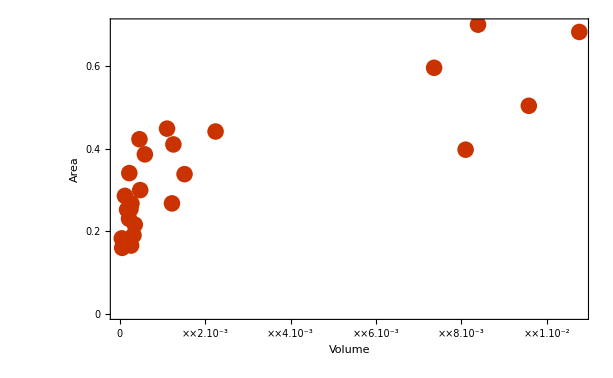

```mathematica
ListPlot[lista2,PlotTheme->"Web",FrameLabel->{{HoldForm[Area],None},{HoldForm[Volume],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```